# Reproduction of the paper in Qeios (v2.0).

```mathematica
nwavesbit = 7;
(* Cantidad de puestos disponibles para rellenar -- *)
binaryT=Table[IntegerString[n,2,nwavesbit],{n,0,(2^nwavesbit-1)}]
Length[binaryT]
```

{0000000,0000001,0000010,0000011,0000100,0000101,0000110,0000111,0001000,0001001,0001010,0001011,0001100,0001101,0001110,0001111,0010000,0010001,0010010,0010011,0010100,0010101,0010110,0010111,0011000,0011001,0011010,0011011,0011100,0011101,0011110,0011111,0100000,0100001,0100010,0100011,0100100,0100101,0100110,0100111,0101000,0101001,0101010,0101011,0101100,0101101,0101110,0101111,0110000,0110001,0110010,0110011,0110100,0110101,0110110,0110111,0111000,0111001,0111010,0111011,0111100,0111101,0111110,0111111,1000000,1000001,1000010,1000011,1000100,1000101,1000110,1000111,1001000,1001001,1001010,1001011,1001100,1001101,1001110,1001111,1010000,1010001,1010010,1010011,1010100,1010101,1010110,1010111,1011000,1011001,1011010,1011011,1011100,1011101,1011110,1011111,1100000,1100001,1100010,1100011,1100100,1100101,1100110,1100111,1101000,1101001,1101010,1101011,1101100,1101101,1101110,1101111,1110000,1110001,1110010,1110011,1110100,1110101,1110110,1110111,1111000,1111001,1111010,1111011,1111100,1111101,1111110,1111111}

128

```mathematica
(* -- Esto es como si fuera 8 Hz --- 3 wavebits*)
(*-- Duración --- *)
stepTime=0.0005;
stepFreq=1/stepTime;
(*Number of points*)
nn=10000;
(*Sample rate*)
sr=550*stepFreq;
(*Time increment*)
dt=1/sr;
df=sr/nn;
binary=Table[IntegerString[n,2,nwavesbit],{n,0,(2^nwavesbit-1)}];
```

Encoding: 1ro lo dividimos

```mathematica
myString="Hello World!";
binaryStringS = StringSplit[myString,""]
binaryStringMap = Table[RandomChoice[binary],{i,1,Length[binaryStringS]}]
binaryString = Table[ToExpression[StringSplit[binaryStringMap[[i]],""]],{i,1,Length[binaryStringMap]}]
(*---*)
(* La frecuencias --*)
SizeString = Length[binaryString];
tinterval=N[sr/2/SizeString];
FreqIn = Table[2π*RandomReal[{i*stepFreq,(i+100)*stepFreq}],{i,1,nwavesbit}]
```

{H,e,l,l,o, ,W,o,r,l,d,!}

{0111001,0100000,1000011,1000010,0110110,1100001,1010110,1101011,0011100,0101010,0101100,0011110}

{{0,1,1,1,0,0,1},{0,1,0,0,0,0,0},{1,0,0,0,0,1,1},{1,0,0,0,0,1,0},{0,1,1,0,1,1,0},{1,1,0,0,0,0,1},{1,0,1,0,1,1,0},{1,1,0,1,0,1,1},{0,0,1,1,1,0,0},{0,1,0,1,0,1,0},{0,1,0,1,1,0,0},{0,0,1,1,1,1,0}}

{337563.,301570.,1.23139×10^6,1.2026×10^6,68716.4,738566.,1.06924×10^6}

```mathematica
myDir=NotebookDirectory[];FreqIn =Import[myDir<>"Freqs_Test1_v3.tex", "List"];
```

```mathematica
(* Arreglos -- *)
SizeElem=SizeString
Array[Awaves8Avark,{SizeString,nwavesbit}];
Array[fwaves8Avark,{SizeString,nwavesbit}];
Array[waves8Avark,{SizeString,nwavesbit}];
Array[Totalwaves8Avark,SizeString];
Array[samples1sec8Avark, SizeString];
Array[Twavesfft8Avark,SizeString];
(* Para los elementos finales de la matriz *)
Array[Totalwaves8Avark2,SizeElem];
Array[samples1sec8Avark2, SizeElem];
Array[Twavesfft8Avark2,SizeElem];
(* Para los elementos finales finales de la matriz *)
Array[Totalwaves8Avark3,1];
Array[samples1sec8Avark3, 1];
Array[Twavesfft8Avark3,1];
```

12

```mathematica
tinterval=N[sr/2/SizeString];
Do[
Do[
Awaves8Avark[i,j]=binaryString[[i]][[j]];
fwaves8Avark[i,j]=ToExpression[FreqIn[[j]]]*Awaves8Avark[i,j];
(*Print[binaryString[[i]][[j]]," : ",fwaves8Avark[i,j]];*)
(* Asi todo el mundo va a ser diferente !! --*)
waves8Avark[i,j]=If[Awaves8Avark[i,j]==0,0,Cos[fwaves8Avark[i,j] *t]];
(*waves8Avark[i,j]=FourierSeries[t/2,t,2];*)
,{j,1,nwavesbit}];(*Print["-----"];*),{i,1,SizeString}]
```

```mathematica
Do[
(*--- Total ---*)
Totalwaves8Avark[i]= Sum[waves8Avark[i,n],{n,1,nwavesbit}];
samples1sec8Avark[i] = Table[N[{t,Totalwaves8Avark[i]}],{t,(i-1)*stepTime,i*stepTime,dt}];
Twavesfft8Avark[i]=Fourier[samples1sec8Avark[i][[All,2]]];
,{i,1,SizeString}]
```

Para ver cuando es más tiempo:

```mathematica
Do[
(*--- Total ---*)
samples1sec8Avark2[i] = Table[N[{t,Totalwaves8Avark[i]}],{t,(i-1),i,dt*100}];
,{i,1,SizeString}]
```

La conformacion de Los 4 elementos:

```mathematica
Totalwaves8Avark[1](*0000000*)
Totalwaves8Avark[2](*001*)
Totalwaves8Avark[3]
Totalwaves8Avark[4]
Totalwaves8Avark[5]
Totalwaves8Avark[6]
```

## Finalmente Concatenamos:

```mathematica
(*-- Aqui se concatenan --*)
Welem =1
Do[
Print[" desde ",Welem*(i-1)+1," : hasta ", Welem*(i-1)+Welem];
(*--- Total ---*)
Totalwaves8Avark3[i]= Join[Table[Totalwaves8Avark[mm],{mm,1,SizeString}]];
samples1sec8Avark3[i] = Table[N[{t,Totalwaves8Avark3[i]}]//Flatten,{t,(i-1)*stepTime,i*stepTime,dt}]//Flatten;
Twavesfft8Avark3[i]=Join[Table[Twavesfft8Avark[mm]//Flatten,{mm,1,SizeString}]]//Flatten
(*Fourier[samples1sec8Avark3[i]];*)
,{i,1,1}]
```

1

desde 1 : hasta 1

{400,400}

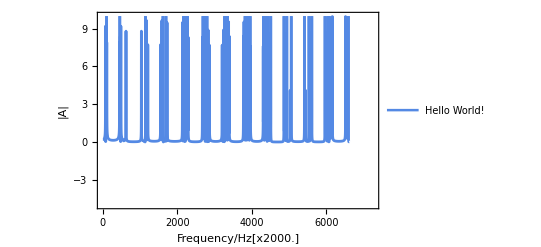

```mathematica
fsz=16;
imgsz={400,400}
ymin=-250;
ymax=2;
xmin=-2;
xmax=sr*stepTime*SizeString*1.1;(*220000*) (*tambien hay información en 11000 *)
yminHz=-5;
ymaxHz=10;
k=1; (*- a -*)
m=2;(*- b -*)
ptTotalIndi8k2=
Column[{ListLinePlot[Abs[(Twavesfft8Avark3[k])],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"Frequency/Hz"<>"[x"<>ToString[stepFreq]<>"]","|A|"},
PlotLegends->Placed[{myString},{0.69,0.12}],
PlotRangePadding->{0.2,.8},
PlotRange->{{xmin,xmax},{yminHz,ymaxHz}},
ImageSize->imgsz]}]
```

{250,250}

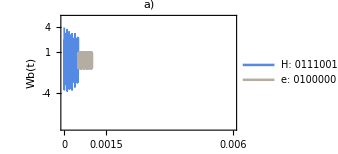
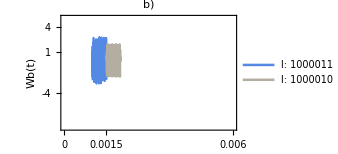
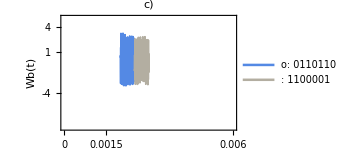
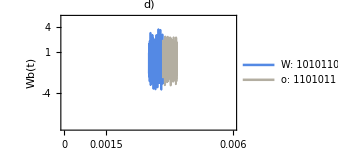
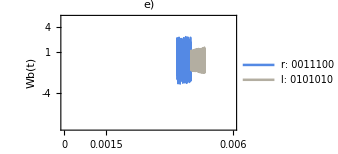
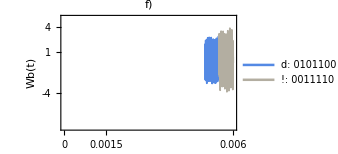

```mathematica
fsz=14;
imgsz={250,250}
ymin=-8.2;
ymax=5.2;
letters={"a)","","b)","","c)","","d)","","e)","","f)"};
ptTotal1=Row[Table[
ListLinePlot[{samples1sec8Avark[m], samples1sec8Avark[m+1]},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
PlotLabel->letters[[m]],
PlotLegends->Placed[{
binaryStringS[[m]]<>": "<>binaryStringMap[[m]],
binaryStringS[[m+1]]<>": "<>binaryStringMap[[m+1]]
},
{0.5,0.2}],
FrameLabel->{"time/s","Wb(t)"},
PlotRange->{{0,SizeString*stepTime},{ymin,ymax}},
FrameTicks->{{{-4,4,1},None},{{0,stepTime*3,stepTime*SizeString},None}},
ImageSize->imgsz],{m,1,5,2}]];
ptTotal2=Row[Table[
ListLinePlot[{samples1sec8Avark[m], samples1sec8Avark[m+1]},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
PlotLabel->letters[[m]],
PlotLegends->Placed[{
binaryStringS[[m]]<>": "<>binaryStringMap[[m]],
binaryStringS[[m+1]]<>": "<>binaryStringMap[[m+1]]
},
{0.5,0.2}],
FrameLabel->{"time/s","Wb(t)"},
PlotRange->{{0,SizeString*stepTime},{ymin,ymax}},
FrameTicks->{{{-4,4,1},None}, {{0,stepTime*3,stepTime*SizeString},None}},
ImageSize->imgsz],{m,7,11,2}]];
ptTotal=Grid[{{ptTotal1},{ptTotal2}}]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Waves_8bits_HelloWorld_v7.png",ptTotal];
```

Decoding?

```mathematica
itest=1;
npuntos=sr;
data=Table[{Range[(itest-1)*sr*stepTime,itest*sr*stepTime][[j]],Abs[(Twavesfft8Avark[itest])][[j]]},{j,1,sr*stepTime/2}];
```

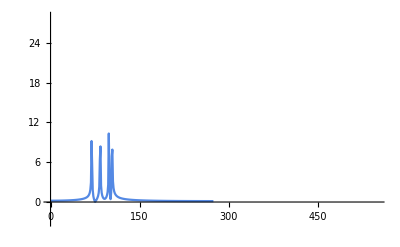

```mathematica
ListLinePlot[data,PlotRange->{{(itest-1)*sr*stepTime,itest*sr*stepTime},{-3,28}}]
```

```mathematica
(*----*)
binaryStringS[[itest]];
binaryStringMap[[itest]];
Totalwaves8Avark[itest];
FreqIn
peaks=FindPeaks[data[[All,2]],1,1,5]
```

{513007.,870613.,1.0482121082694172*^6,1.2331338086689976*^6,264985.,869858.,1.297988877870819*^6}

{{70,9.19945},{85,8.38921},{99,10.3355},{105,7.91176}}

```mathematica
(*----*)
binaryStringS[[itest]]
Print["Mapa"];
binaryStringMap[[itest]]
decod1=Table[If[Abs[2π*N[peaks[[k,1]]]*stepFreq-fwaves8Avark[itest,i]]<15*stepFreq
,1,0],{k,1,Length[peaks]},{i,1,nwavesbit}]
Print["Decodificado"];
Sum[decod1[[i]],{i,1,Length[decod1]}]
```

H

Mapa

0111001

{{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,0,1}}

Decodificado

{0,1,1,1,0,0,1}

Hacer un diagrama cool de esta metodologia.

Cos[264985. t]+Cos[1.04821×10^6 t]+Cos[1.23313×10^6 t]

{0,0,1,1,1,0,0}

r

0011100

{513007.,870613.,1.0482121082694172*^6,1.2331338086689976*^6,264985.,869858.,1.297988877870819*^6}

{276460.,1.06814×10^6,1.24407×10^6}

{0,0,1,1,1,0,0}

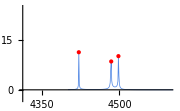

```mathematica
itest=9;
Totalwaves8Avark[itest]
npuntos=sr;
rango=Range[(itest-1)*sr*stepTime,itest*sr*stepTime];
data=Table[{rango[[j]],Abs[(Twavesfft8Avark[itest])][[j]]},{j,1,sr*stepTime/2}];
(*----*)
binaryString[[itest]]
binaryStringS[[itest]]
binaryStringMap[[itest]]
Totalwaves8Avark[itest];
FreqIn
peaks=FindPeaks[data[[All,2]],1,1,5];
Table[N[2π*peaks[[k,1]]]*stepFreq,{k,1,Length[peaks]}]
(*----*)
decod1=Table[If[Abs[2π*N[peaks[[k,1]]]*stepFreq-fwaves8Avark[itest,i]]<15*stepFreq,1,0],{k,1,Length[peaks]},{i,1,nwavesbit}];
SumDecod=Sum[decod1[[i]],{i,1,Length[decod1]}]
SumDecod=Table[If[SumDecod[[i]]>1,1,SumDecod[[i]]],{i,1,Length[SumDecod]}];
(*----*)
DecodFinal=If[SumDecod==binaryString[[itest]],binaryStringS[[itest]],"Unknown!"];
(*----*)
ListLinePlot[
data,
PlotStyle->{{Thickness@0.003, Blue@Darker}},PlotLegends->Placed[{DecodFinal},
{0.82,0.95}],
ImageSize->Small,
(*PlotRange->{{(itest-1)*sr,(itest-1)*sr+0.05*Abs[(itest-1)*sr-itest*sr]},{-3,48}},*)
PlotRange->{{rango[[1]]*0.98,(peaks[[Length[peaks]]][[1]]+(itest-1)*sr*stepTime-1)+100},{-3,25}},
Epilog->Table[{Text[Style["",10],
{peaks[[l]][[1]]+(itest-1)*sr*stepTime-1,
peaks[[l]][[2]]*1.18}],
Red,PointSize[Medium],
Point@{peaks[[l]][[1]]+(itest-1)*sr*stepTime-1,
peaks[[l]][[2]]}},{l,1,Length[peaks]}]
]
```

Conclusion: El cambio de amplitud en las ondas afecta el grosor de los picos de frecuencia.

### Entonces la pregunta es: como es o queda

{450,450}

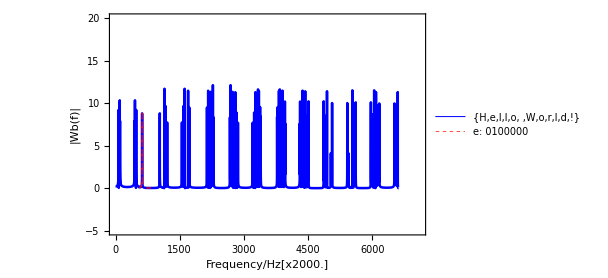

```mathematica
fsz=16;
imgsz={450,450}
ymin=-4;
ymax=4;
xmin=-500;
xmax=sr*SizeString*stepTime+500; (*tambien hay información en 11000 *)
yminHz=-5;
ymaxHz=20;
k=1; (*- a -*)
m=2;(*- 1, no tiene solucion  -- b -*)
ptHelloWHv1=Show[{ListLinePlot[{
Abs[(Twavesfft8Avark3[k])],Table[{Range[(m-1)*sr*stepTime,m*sr*stepTime][[j]]+m,Abs[(Twavesfft8Avark[m])][[j]]},{j,1,sr*stepTime/2}]
},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{
{Thickness@0.004, Blue},
{Thickness@0.002,Red, Dashed}},
FrameLabel->{"Frequency/Hz"<>"[x"<>ToString[stepFreq]<>"]","|Wb(f)|"},
PlotLegends->Placed[{binaryStringS,binaryStringS[[m]]<>": "<>binaryStringMap[[m]]},{0.5,0.82}],
PlotRange->{{0,xmax},{yminHz,ymaxHz}},
ImageSize->imgsz]}, Padding->0]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Waves_8bits_Hello_v7.pdf",ptHelloWHv1];
```

{600,600}

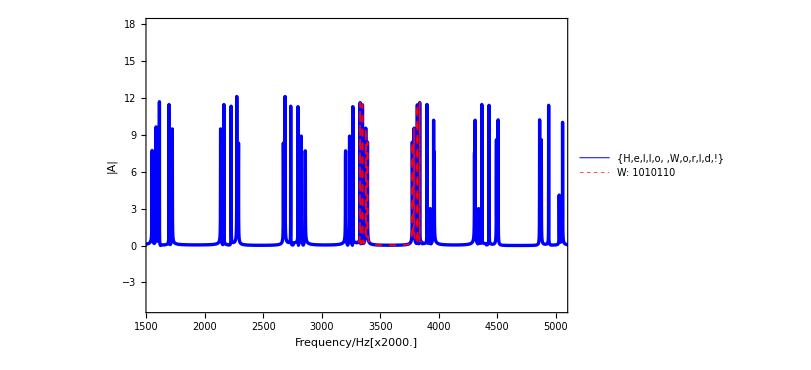

```mathematica
fsz=16;
imgsz={600,600}
ymin=-4;
ymax=4;
xmin=-500;
xmax=sr*SizeString*stepTime+500; 
(*tambien hay información en 11000 *)
yminHz=-5;
ymaxHz=18;
k=1; (*- a -*)
m=7;(*- 1, no tiene solucion  -- b -*)
ptTotalIndi8k2=
Column[{ListLinePlot[{
Abs[(Twavesfft8Avark3[k])],Table[{Range[(m-1)*sr*stepTime,m*sr*stepTime][[j]]+m,Abs[(Twavesfft8Avark[m])][[j]]},{j,1,sr*stepTime}]
},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{
{Thickness@0.004, Blue},
{Thickness@0.002,Red, Dashed}},
FrameLabel->{"Frequency/Hz"<>"[x"<>ToString[stepFreq]<>"]","|A|"},
PlotLegends->Placed[{binaryStringS,binaryStringS[[m]]<>": "<>binaryStringMap[[m]]},{0.5,0.82}],
PlotRange->{{(m-1)*sr*stepTime-6.3*Abs[(m-1)*sr*stepTime-m*sr*stepTime]/2,(m-1)*sr*stepTime+6.3*Abs[(m-1)*sr*stepTime-m*sr*stepTime]/2},{yminHz,ymaxHz}},
ImageSize->imgsz]}]
```

{600,600}

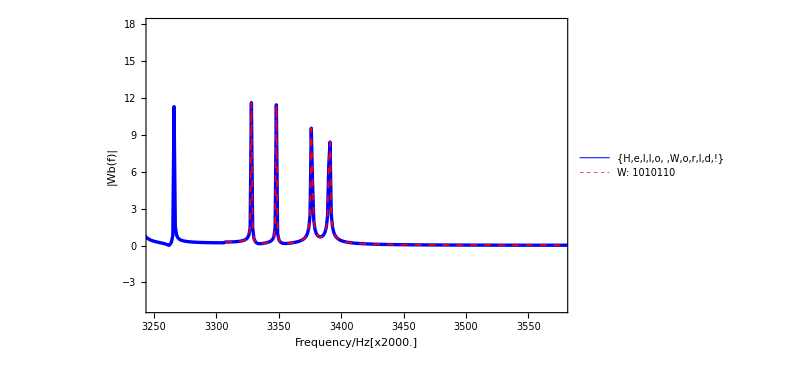

```mathematica
fsz=16;
imgsz={600,600}
ymin=-4;
ymax=4;
xmin=-500;
xmax=sr*SizeString*stepTime+500; (*tambien hay información en 11000 *)
yminHz=-5;
ymaxHz=18;
k=1; (*- a -*)
m=7;(*- 1, no tiene solucion  -- b -*)
ptOneletterandHellov1=
Column[{ListLinePlot[{
Abs[(Twavesfft8Avark3[k])],Table[{Range[(m-1)*sr*stepTime,m*sr*stepTime][[j]]+m,Abs[(Twavesfft8Avark[m])][[j]]},{j,1,sr*stepTime}]
},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{
{Thickness@0.004, Blue},
{Thickness@0.002,Red, Dashed}},
FrameLabel->{"Frequency/Hz"<>"[x"<>ToString[stepFreq]<>"]","|Wb(f)|"},
PlotLegends->Placed[{binaryStringS,binaryStringS[[m]]<>": "<>binaryStringMap[[m]]},{0.7,0.82}],
PlotRange->{{(m-1)*sr*stepTime-50,(m-1)*sr*stepTime+0.5*Abs[(m-1)*sr*stepTime-m*sr*stepTime]},{yminHz,ymaxHz}},
ImageSize->imgsz]}]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Waves_OneLetter_Hello_v7.pdf",ptOneletterandHellov1];
```

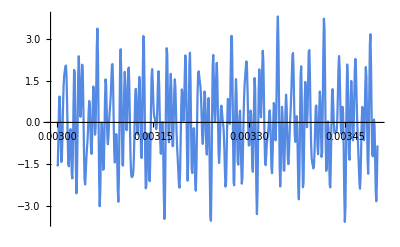

```mathematica
ListLinePlot[samples1sec8Avark[m]]
```

{200,200}

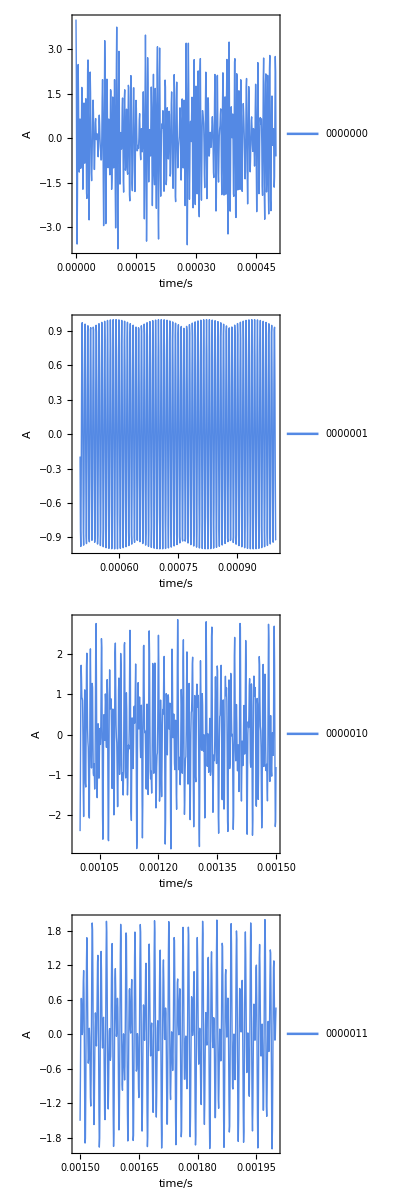
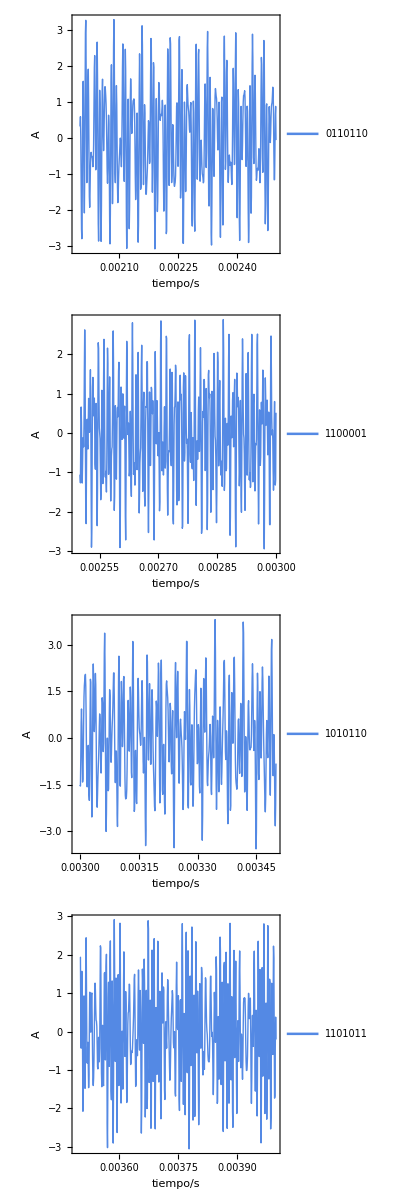

```mathematica
fsz=14;
imgsz={200,200}
ymin=-5;
ymax=5;
ptTotal=Style[Row[{{Column[Table[ListLinePlot[samples1sec8Avark[m],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"time/s","A"},
(*PlotLegends->{"from binary = "<>binary[[m]]},*)
PlotLegends->Placed[{""<>binary[[m]]},{0.69,0.2}],
(*PlotRange->{{(m-1)*sr*dt*stepTime,(m-1)*sr*dt*stepTime+0.5},{ymin,ymax}},*)
ImageSize->imgsz],{m,1,4}]]},
(*-- Otra mitad --*)
Column[Table[ListLinePlot[samples1sec8Avark[m],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"tiempo/s","A"},
PlotLegends->Placed[{""<>binaryStringMap[[m]]},{0.69,0.2}],
(*PlotRange->{{(m-1)*sr*dt*stepTime,(m-1)*sr*dt*stepTime+0.5},{ymin,ymax}},*)
ImageSize->imgsz],{m,5,8}]]
}]]
```

## Individuales:

{800,300}

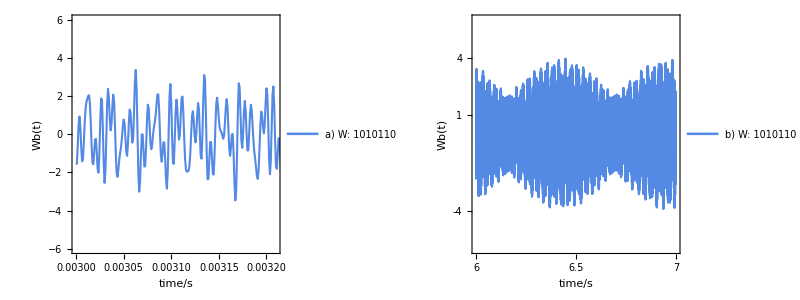

```mathematica
fsz=14;
imgsz={300,300};
imgsz2={800,300}
ymin=-6;
ymax=6;
mm=7;
ptIndi2Rowa=Grid[{{ListLinePlot[samples1sec8Avark[mm],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"time/s","Wb(t)"},
PlotLegends->Placed[{"a) "<>""<>binaryStringS[[mm]]<>": "<>binaryStringMap[[mm]]},{0.6,0.9}],
PlotRange->{{(mm-1)*stepTime,(mm-1)*stepTime+(mm-1)*stepTime*0.07},{ymin,ymax}},
(*FrameTicks->{{{-4,4,1},None},{{0,stepTime*4,stepTime*SizeString*0.8},None}},*)
ImageSize->imgsz],
ListLinePlot[samples1sec8Avark2[mm],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"time/s","Wb(t)"},
PlotLegends->Placed[{"b) "<>""<>binaryStringS[[mm]]<>": "<>binaryStringMap[[mm]]},{0.6,0.9}],
PlotRange->{{6,7},{ymin,ymax}},
FrameTicks->{{{-4,4,1},None},{{6,6.5,7},None}},
ImageSize->imgsz]}}]
```

{640,250}

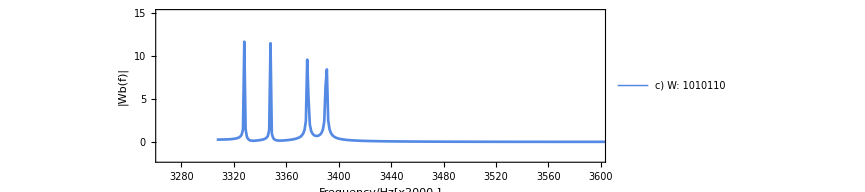

```mathematica
fsz=16;
imgsz={300,300};
imgsz2={640,250}
mm=7;
ymin=-2;
ymax=4;
xmin=10300;
xmax=10700; (*tambien hay información en 11000 *)
yminHz=-2;
ymaxHz=15;

ptIndi2Rowb=
ListLinePlot[Table[{Range[(mm-1)*sr*stepTime,mm*sr*stepTime][[j]]+mm,Abs[(Twavesfft8Avark[mm])][[j]]},{j,1,sr*stepTime}],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.003, Blue@Darker}},
FrameLabel->{"Frequency/Hz"<>"[x"<>ToString[stepFreq]<>"]","|Wb(f)|"},
(* -- *)
PlotLegends->Placed[{"c) "<>""<>binaryStringS[[mm]]<>": "<>binaryStringMap[[mm]]},{0.75,0.9}],
PlotRange->{{(mm-1)*sr*stepTime*0.99,(mm-1)*sr*stepTime*0.99+0.6*Abs[(mm-1)*sr*stepTime-mm*sr*stepTime]},{yminHz,ymaxHz}},
AspectRatio->0.3,
ImageSize->imgsz2]
```

```mathematica
ptIndiTotaln7=Grid[{{ptIndi2Rowa},{ptIndi2Rowb}}]
```

-Graphics-
-Graphics-

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Waves_128bits_Indi_variable_v7.png",ptIndiTotaln7];
```

{800,300}

{a) ,b) ,c) ,d) }

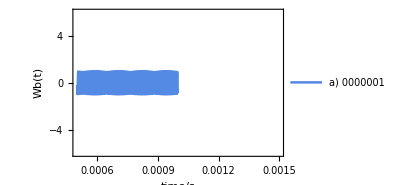
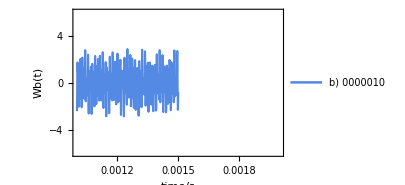
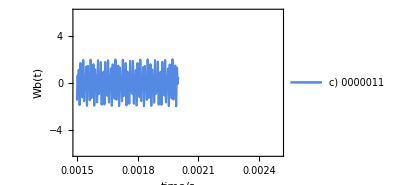
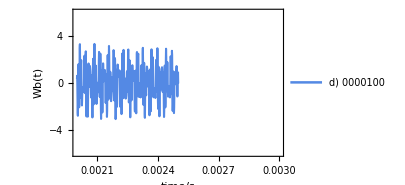

```mathematica
fsz=14;
imgsz={300,300};
imgsz2={800,300}
ymin=-6;
ymax=6;
mm=4;
strings={"a) ","b) ","c) ","d) "}
pt4wavesRows=Row[Table[ListLinePlot[
samples1sec8Avark[mm],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
FrameLabel->{"time/s","Wb(t)"},
(*PlotLegends->{"from binary = "<>binary[[m]]},*)
PlotLegends->Placed[{strings[[mm-1]]<>binary[[mm]]},{0.75,0.9}],
PlotRange->{{(mm-1)*sr*dt*stepTime,(mm-1)*sr*dt*stepTime+0.001},{ymin,ymax}},
ImageSize->imgsz],{mm,2,5}]]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Waves_8bits_4waves_variable_v4.png",pt4wavesRows];
```

Decodificando:

```mathematica
Clear[ptDecod]
```

```mathematica
Array[ptDecod,2]
```

{ptDecod[1],ptDecod[2]}

```mathematica
binaryStringS
```

{H,e,l,l,o, ,W,o,r,l,d,!}

{250,250}

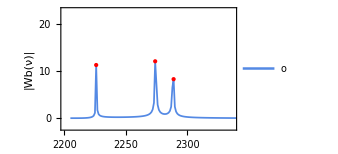

```mathematica
fsz=10;
imgsz={250,250}
yminHz=-2;
ymaxHz=23;
letters={"a)","","b)","","c)","","d)","","e)","","f)"};
m=5;
data=Table[{Range[(m-1)*sr*stepTime,m*sr*stepTime][[j]]+(m),Abs[(Twavesfft8Avark[m])][[j]]},{j,1,sr*stepTime/2}];
peaks=FindPeaks[data[[All,2]],1,1,5];
p5=ListLinePlot[{Table[{Range[((m)-1)*sr*stepTime,(m)*sr*stepTime][[j]]+(m),Abs[(Twavesfft8Avark[(m)])][[j]]},{j,1,sr*stepTime}]},
(*--*)
Epilog->Table[{Text[Style["",10],{peaks[[l]][[1]]+((m)-1)*sr*stepTime+1,peaks[[l]][[2]]*1.18}],Red,PointSize[Large],Point@{peaks[[l]][[1]]+((m)-1)*sr*stepTime+m-1,peaks[[l]][[2]]}},{l,1,Length[peaks]}],
(*--*)
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.005, Blue@Darker}},
(*PlotLabel->letters[[m]],*)
PlotLegends->Placed[{
binaryStringS[[m]],
binaryStringS[[m+1]]
},
{0.8,0.85}],
FrameLabel->{"Frequency/Hz"<>"[x2000]","|Wb(ν)|"},
PlotRange->{{(m-1)*sr*stepTime,(m-1)*sr*stepTime+0.5*Abs[(m-1)*sr*stepTime-m*sr*stepTime]/2},
{yminHz,ymaxHz}},
ImageSize->imgsz]
```

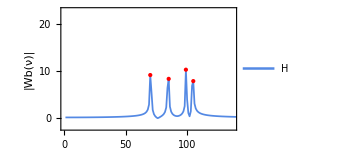
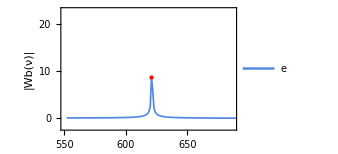
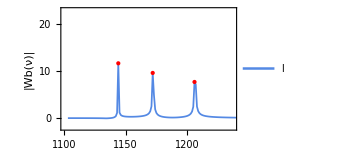
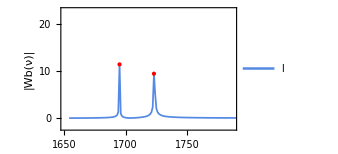
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
ptDecodHellov4=Grid[{{p1,p2},{p3,p4},{p5}}]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Decodifying_8bits_HelloW_v6_Paper.png",ptDecodHellov4];
```

La onda completa:

{640,250}

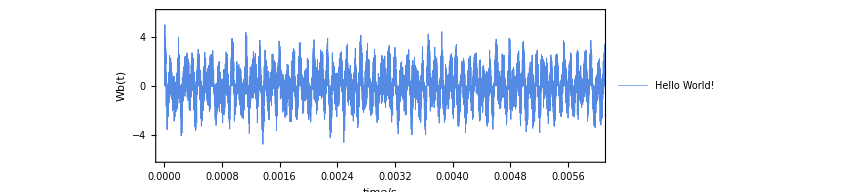

```mathematica
fsz=16;
imgsz={300,300};
imgsz2={640,250}
mm=7;
ymin=-6;
ymax=6;
xmin=10300;
xmax=10700; (*tambien hay información en 11000 *)
yminHz=-2;
ymaxHz=32;

ptTotalWave2=
ListLinePlot[Table[{i*dt,samples1sec8Avark3[1][[i]]},{i,1,Length[samples1sec8Avark3[1]]}],
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,fsz],
PlotStyle->{{Thickness@0.001, Blue@Darker}},
FrameLabel->{"time/s","Wb(t)"},
(* -- *)
PlotLegends->Placed[{"Hello World!"},{0.75,0.9}],
AspectRatio->0.3,
PlotRange->{{0,SizeString*stepTime},{ymin,ymax}},
ImageSize->imgsz2]
```

```mathematica
myDir=NotebookDirectory[];
Export[myDir<>"/Decodifying_Total_HelloW_v5.png",ptTotalWave2];
```